```mathematica
SetDirectory@SystemDialogInput@"Directory"
```

D:\大创\prog2\result

```mathematica
TextOri="0.40 \t 0.45 \t 7.6679 \t 0.00870 \t 0.92689 
0.45 \t 0.50 \t 7.1124 \t 0.00796 \t 0.69189 
0.50 \t 0.55 \t 6.6389 \t 0.00738 \t 0.57433 
0.55 \t 0.60 \t 6.2556 \t 0.00693 \t 0.51175 
0.60 \t 0.65 \t 5.8920 \t 0.00650 \t 0.47001 
0.65 \t 0.70 \t 5.4943 \t 0.00606 \t 0.43340 
0.70 \t 0.75 \t 5.1139 \t 0.00567 \t 0.40139 
0.75 \t 0.80 \t 4.6603 \t 0.00523 \t 0.36501 
0.60 \t 0.70 \t 5.6473 \t 0.00563 \t 0.44747 
0.70 \t 0.80 \t 4.8108 \t 0.00480 \t 0.37712 
0.80 \t 0.90 \t 4.0220 \t 0.00412 \t 0.31475 
0.90 \t 1.00 \t 3.3034 \t 0.00353 \t 0.25875 
1.00 \t 1.10 \t 2.6646 \t 0.00302 \t 0.20934 
1.10 \t 1.20 \t 2.1118 \t 0.00257 \t 0.16701 
1.20 \t 1.30 \t 1.6427 \t 0.00218 \t 0.13172 
1.30 \t 1.40 \t 1.2511 \t 0.00183 \t 0.10323 
1.40 \t 1.50 \t 0.9361 \t 0.00153 \t 0.08171 
1.50 \t 1.60 \t 0.6884 \t 0.00127 \t 0.06660 
1.60 \t 1.70 \t 0.5020 \t 0.00104 \t 0.05744 
1.70 \t 1.80 \t 0.3612 \t 0.00086 \t 0.04133 
1.80 \t 1.90 \t 0.2618 \t 0.00071 \t 0.02995 
1.90 \t 2.00 \t 0.1870 \t 0.00058 \t 0.02140 ";
```

```mathematica
ListOri=ToExpression@StringSplit[StringSplit[TextOri,"\n"],"\t"];
ListOri=Drop[ListOri,None,-2]
ListOri={(#[[1]]+#[[2]])/2,#[[3]]}&/@ListOri
ListOri1=Drop[ListOri,{9,-1}]
ListOri2=Drop[ListOri,8]
```

{{0.4,0.45,7.6679},{0.45,0.5,7.1124},{0.5,0.55,6.6389},{0.55,0.6,6.2556},{0.6,0.65,5.892},{0.65,0.7,5.4943},{0.7,0.75,5.1139},{0.75,0.8,4.6603},{0.6,0.7,5.6473},{0.7,0.8,4.8108},{0.8,0.9,4.022},{0.9,1.,3.3034},{1.,1.1,2.6646},{1.1,1.2,2.1118},{1.2,1.3,1.6427},{1.3,1.4,1.2511},{1.4,1.5,0.9361},{1.5,1.6,0.6884},{1.6,1.7,0.502},{1.7,1.8,0.3612},{1.8,1.9,0.2618},{1.9,2.,0.187}}

{{0.425,7.6679},{0.475,7.1124},{0.525,6.6389},{0.575,6.2556},{0.625,5.892},{0.675,5.4943},{0.725,5.1139},{0.775,4.6603},{0.65,5.6473},{0.75,4.8108},{0.85,4.022},{0.95,3.3034},{1.05,2.6646},{1.15,2.1118},{1.25,1.6427},{1.35,1.2511},{1.45,0.9361},{1.55,0.6884},{1.65,0.502},{1.75,0.3612},{1.85,0.2618},{1.95,0.187}}

{{0.425,7.6679},{0.475,7.1124},{0.525,6.6389},{0.575,6.2556},{0.625,5.892},{0.675,5.4943},{0.725,5.1139},{0.775,4.6603}}

{{0.65,5.6473},{0.75,4.8108},{0.85,4.022},{0.95,3.3034},{1.05,2.6646},{1.15,2.1118},{1.25,1.6427},{1.35,1.2511},{1.45,0.9361},{1.55,0.6884},{1.65,0.502},{1.75,0.3612},{1.85,0.2618},{1.95,0.187}}

```mathematica
SystemDialogInput@"FileOpen"
```

D:\大创\prog2\Start2\dNptdpt_AuAu39 _p1_c025.txt

```mathematica
ListFit=Import@"D:\\大创\\prog2\\Start2\\dNptdpt_AuAu39 _p1_c025.txt";
ListFit=StringReplace[#,"E"->"*10^"]&/@ StringSplit[#,"    "]&/@StringSplit[ListFit,"\n"][[2;;-1]]//ToExpression;
ListS=Table[{ListFit[[i,1]],Total[ListFit[[i]][[3;;-2]]]},{i,1,Length@ListFit}]
ListFit=Drop[ListFit,None,{2,-2}]
```

{{0.65,0.353154},{0.75,0.2772},{0.85,0.214573},{0.95,0.164565},{1.05,0.125437},{1.15,0.0952288},{1.25,0.0721143},{1.35,0.0545334},{1.45,0.0412135},{1.55,0.0311463},{1.65,0.0235478},{1.75,0.0178158},{1.85,0.013492},{1.95,0.0102289}}

{{0.65,6.36778},{0.75,5.36954},{0.85,4.36769},{0.95,3.45649},{1.05,2.67739},{1.15,2.03889},{1.25,1.5315},{1.35,1.13755},{1.45,0.83715},{1.55,0.611346},{1.65,0.443564},{1.75,0.320071},{1.85,0.229889},{1.95,0.164463}}

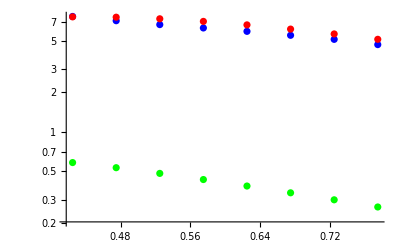

```mathematica
{ListFit1=ListFit,ListS1=ListS};
ListLogPlot[{ListOri1,ListFit1,ListS1},PlotStyle->{Blue,Red,Green},PlotRange->Full]
```

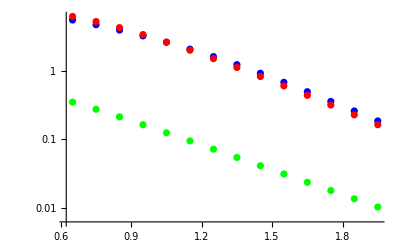

```mathematica
{ListFit2=ListFit,ListS2=ListS};
ListLogPlot[{ListOri2,ListFit2,ListS2},PlotStyle->{Blue,Red,Green},PlotRange->Full]
```

```mathematica
Export["AuAu39_fit.dat",N[#,4]&@Rationalize@ListOri1]
```

AuAu39_fit.dat